```mathematica
re=1/(So (n/(n+1) (1/Fr^2)^(1/n) (1-B)^((n+1)/n) (1-n/(2 n+1) (1-B)))^n)
```

((((1-B)^((1+n)/n) (1/Fr^2)^(1/n) n (1-((1-B) n)/(1+2 n)))/(1+n))^-n)/So

```mathematica
rePL=re/.{B->0, n->0.129, So->0.06}
```

22.3584/(((1/Fr^2)^7.75194)^0.129)

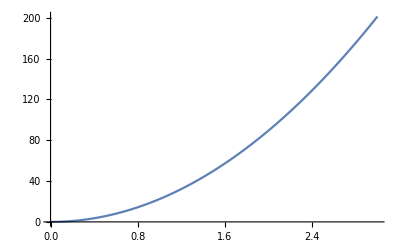

```mathematica
Plot[rePL, {Fr, 0,3}]
```

```mathematica
rePLVal=re/.{B->0, n->0.129, So->0.06, Fr->0.75}
```

12.5766